```mathematica
"Questo file è necessario per fare l'analisi dati della quarta esperienza di fisica ottica: l'effetto Faraday. L'analisi dati è atta al raggiungimento di due scopi diversi:
-Stima della costante di Verdet
-Stima della relazione tra la lunghezza d'onda e la costante di Verdet
Entrambe le stime andranno fatte con un approccio di tipo grafico, utilizzando interpolazioni (in particolare il comando NonlienarModelFit), saranno ovviamente importati i dati e si alvorerà con grafici"
```

Questo file è necessario per fare l'analisi dati della quarta esperienza di fisica ottica: l'effetto Faraday. L'analisi dati è atta al raggiungimento di due scopi diversi:
-Stima della costante di Verdet
-Stima della relazione tra la lunghezza d'onda e la costante di Verdet
Entrambe le stime andranno fatte con un approccio di tipo grafico, utilizzando interpolazioni (in particolare il comando NonlienarModelFit), saranno ovviamente importati i dati e si alvorerà con grafici

## Costante di Verdet

```mathematica
(*"Per stimare la costante di Verdet conviene utilizzare la legge di Malus:"*)
Itheta[Io_ , theta_] := Io (Cos[theta Degree])^2
```

```mathematica
Litterbio = 0.11
```

0.11

```mathematica
(*Risulta inoltre opportuno andare a utilizzare la legge che caratterizza la birifrangenza magnetica, i cui Natali si danno storicamente a Faraday (da cui prende il nome l'effetto)*)
V[B_,deltatheta_] := deltatheta /(B * Litterbio)
```

```mathematica
(*Per stimare la costante di Verdet, risulta quindi andare a conoscere tutte le caratteristiche dell'esperimento. Per quanto riguarda la B e la L, esse sono registrate dal laboratorio (per quanto riguarda la L) o di facile stima (legge dei solenoidi per quanto riguarda la B), il parametro di più difficile interpretazione è deltatheta, per stimare il quale è necessario interpolare alcune funzioni. Dalla legge di Malus risulta possibile, andando a operare tramite interpolazioni, stimare la Io e quale sia effettivamente l'angolo nel nostro sistema di riferimento tale che la corresnte registrata dall'analizzatore abbia valore massimo. Si inizino i calcoli veri e propri, Importando tutti i dati:*)
```

```mathematica
(*Per quanto riguarda il modo con cui i dati vengoo registrati, si utilizzi la lettera (rgb) seguita dal numero di ampere*)
```

```mathematica
b0 = Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/blu_0_ampere.xls"];
b1 = Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/blu_1_ampere.xls"];
b15 =Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/blu_1.5_ampere.xls"];
b2 = Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/blu_2_ampere.xls"];
b3 =Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/blu_3_ampere.xls"];
g0 =Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/giallo_0_ampere.xls"];
g1 =Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/giallo_1_ampere.xls"];
g15 =Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/giallo_1.5_ampere.xls"];
g2 =Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/giallo_2_ampere.xls"];
g3 =Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/giallo_3_ampere.xls"];
r0 =Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/rosso_0_ampere.xls"];
r1 =Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/rosso_1_ampere.xls"];
r15 =Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/rosso_1.5_ampere.xls"];
r2 =Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/rosso_2_ampere.xls"];
r3 =Import["/home/davide/Dropbox/Laboratorio/Ottica_Fisica/04_Faraday/dati_formattati/rosso_3_ampere.xls"];
```

## Blu

### BLU 0 & 1

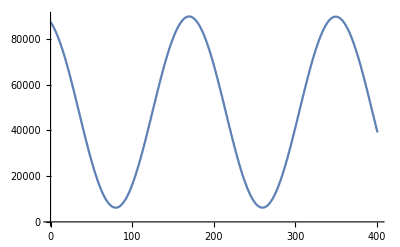

```mathematica
llpb = ListLinePlot[b0] (*Il listlineplot ti permette di plottare coppie di dati su un grafico, tanto alla fine i grafici li fo con GNUplot*)
```

```mathematica
nlmb0 =NonlinearModelFit[b0,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6243.3+83528.4 Cos[° (370.068+theta)]^2]

```mathematica
FittedModel[6243.299221715556+83528.36162613297 Cos[° (370.06848083361547+theta)]^2](*Funzione che descrive l'andamento di b0*)
```

FittedModel[6243.3+83528.4 Cos[° (370.068+theta)]^2]

```mathematica
nlmgraphb0 = 6243.299221715556+83528.36162613297 Cos[° (370.06848083361547+theta)]^2
```

6243.3+83528.4 Cos[° (370.068+theta)]^2

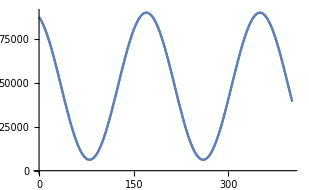

```mathematica
Show[Plot[nlmgraphb0,{theta,0,400}],ListLinePlot[{b0}]]
```

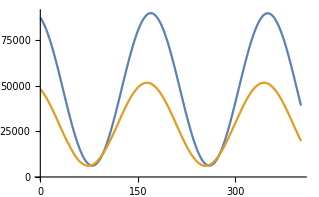

```mathematica
ListLinePlot[{b0,b1}]
```

```mathematica
nlmb1 =NonlinearModelFit[b1,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6152.95+45501.7 Cos[° (915.973+theta)]^2]

```mathematica
FittedModel[6152.952808475714+45501.714113517315 Cos[° (915.9727402681748+theta)]^2](*Funzione che descrive l'andamento di b1*)
```

FittedModel[6152.95+45501.7 Cos[° (915.973+theta)]^2]

```mathematica
nlmgraphb1 = 6152.952808475714+45501.714113517315 Cos[° (915.9727402681748+theta)]^2
```

6152.95+45501.7 Cos[° (915.973+theta)]^2

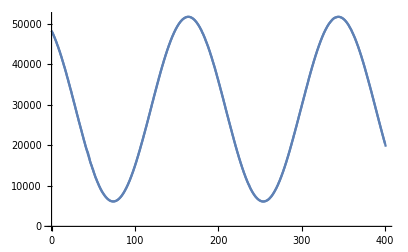

```mathematica
Show[Plot[nlmgraphb1,{theta,0,400}],ListLinePlot[{b1}]]
```

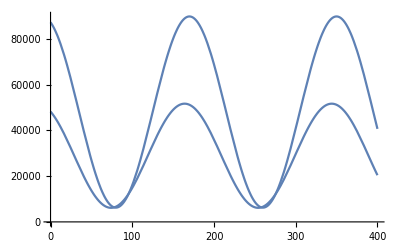

```mathematica
Show[Plot[nlmgraphb0,{theta,0,400}],Plot[nlmgraphb1,{theta,0,400}]]
```

```mathematica
915.9727402681748-370.06848083361547
```

545.904

```mathematica
deltathetab01 = 545.904 -(360+180)
```

5.904

### BLU 1.5

```mathematica
nlmb15 =NonlinearModelFit[b15,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6731.25+84048.4 Cos[° (1458.81+theta)]^2]

```mathematica
FittedModel[6731.25339471394+84048.4491792789 Cos[° (1458.8096099635727+theta)]^2](*Funzione che descrive l'andamento di b1.5*)
```

FittedModel[6731.25+84048.4 Cos[° (1458.81+theta)]^2]

```mathematica
nlmgraphb15 = 6731.25339471394+84048.4491792789 Cos[° (1458.8096099635727+theta)]^2
```

6731.25+84048.4 Cos[° (1458.81+theta)]^2

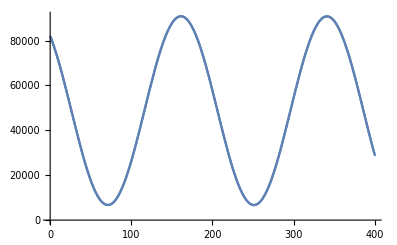

```mathematica
Show[Plot[nlmgraphb15,{theta,0,400}],ListLinePlot[{b15}]]
```

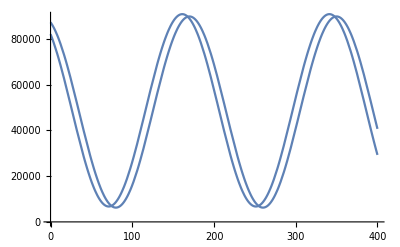

```mathematica
Show[Plot[nlmgraphb0,{theta,0,400}],Plot[nlmgraphb15,{theta,0,400}]]
```

```mathematica
1458.8096099635727-370.06848083361547
```

1088.74

```mathematica
deltathetab015 = 1088.7411291299572 -(360+360+360)
```

8.74113

### BLU 2

```mathematica
nlmb2 =NonlinearModelFit[b2,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6349.26+83199.9 Cos[° (1461.08+theta)]^2]

```mathematica
FittedModel[6349.255513359317+83199.93551976306 Cos[° (1461.0836699759482+theta)]^2](*Funzione che descrive l'andamento di b2*)
```

```mathematica
nlmgraphb2 = 6349.255513359317+83199.93551976306 Cos[° (1461.0836699759482+theta)]^2
```

6349.26+83199.9 Cos[° (1461.08+theta)]^2

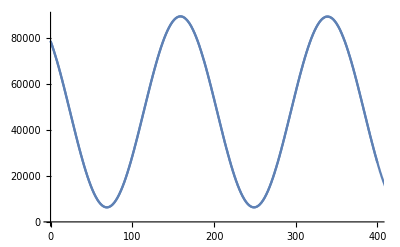

```mathematica
Show[Plot[nlmgraphb2,{theta,0,400}],ListLinePlot[{b2}]]
```

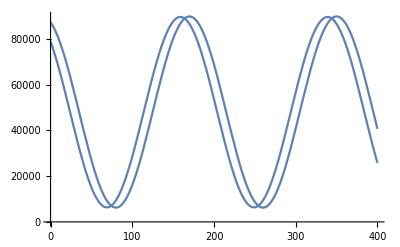

```mathematica
Show[Plot[nlmgraphb0,{theta,0,400}],Plot[nlmgraphb2,{theta,0,400}]]
```

```mathematica
1461.0836699759482-370.06848083361547
```

1091.02

```mathematica
deltathetab02 = 1091.0151891423327 -(360+360+360)
```

11.0152

### BLU 3

```mathematica
nlmb3 =NonlinearModelFit[b3,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6448.48+82349. Cos[° (2185.81+theta)]^2]

```mathematica
FittedModel[6448.477653951516+82348.95078410635 Cos[° (2185.8089929105163+theta)]^2](*Funzione che descrive l'andamento di b3*)
```

```mathematica
nlmgraphb3 = 6448.477653951516+82348.95078410635 Cos[° (2185.8089929105163+theta)]^2
```

6448.48+82349. Cos[° (2185.81+theta)]^2

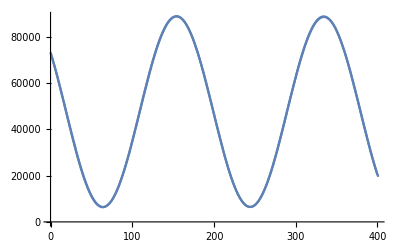

```mathematica
Show[Plot[nlmgraphb3,{theta,0,400}],ListLinePlot[{b3}]]
```

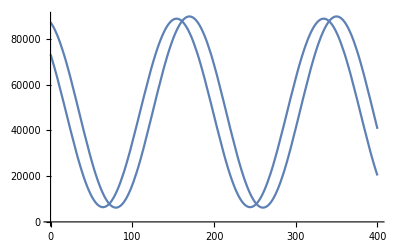

```mathematica
Show[Plot[nlmgraphb0,{theta,0,400}],Plot[nlmgraphb3,{theta,0,400}]]
```

```mathematica
2185.8089929105163-370.06848083361547
```

1815.74

```mathematica
deltathetab03 =1815.7405120769008-(360+360+360+360+360)
```

15.7405

## Giallo

### GIALLO 0

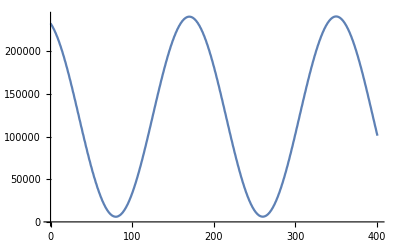

```mathematica
llpg = ListLinePlot[g0]
```

```mathematica
nlmg0 =NonlinearModelFit[g0,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6082.78+234754. Cos[° (370.058+theta)]^2]

```mathematica
FittedModel[6082.7768053115915+234753.93933825294 Cos[° (370.05825107862717+theta)]^2](*Funzione che descrive l'andamento di g0*)
```

FittedModel[6082.78+234754. Cos[° (370.058+theta)]^2]

```mathematica
nlmgraphg0 = 6082.7768053115915+234753.93933825294 Cos[° (370.05825107862717+theta)]^2
```

6082.78+234754. Cos[° (370.058+theta)]^2

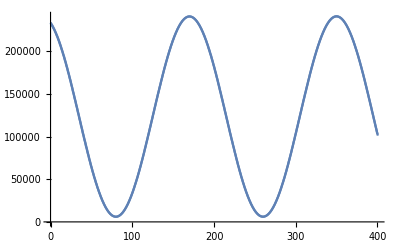

```mathematica
Show[Plot[nlmgraphg0,{theta,0,400}],ListLinePlot[{g0}]]
```

### GIALLO 1

```mathematica
nlmg1 =NonlinearModelFit[g1,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6276.88+235824. Cos[° (913.555+theta)]^2]

```mathematica
FittedModel[6276.878215453928+235824.2132141684 Cos[° (913.5547697209057+theta)]^2](*Funzione che descrive l'andamento di g1*)
```

FittedModel[6276.88+235824. Cos[° (913.555+theta)]^2]

```mathematica
nlmgraphg1 = 6276.878215453928+235824.2132141684 Cos[° (913.5547697209057+theta)]^2
```

6276.88+235824. Cos[° (913.555+theta)]^2

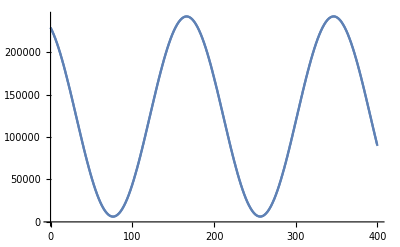

```mathematica
Show[Plot[nlmgraphg1,{theta,0,400}],ListLinePlot[{g1}]]
```

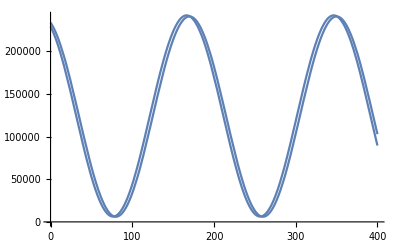

```mathematica
Show[Plot[nlmgraphg0,{theta,0,400}],Plot[nlmgraphg1,{theta,0,400}]]
```

```mathematica
913.5547697209057-370.05825107862717
```

543.497

```mathematica
deltathetag01 = 543.4965186422785 -(360+180)
```

3.49652

### GIALLO 1.5

```mathematica
nlmg15 =NonlinearModelFit[g15,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6662.85+238017. Cos[° (550.748+theta)]^2]

```mathematica
FittedModel[6662.851367541711+238016.74957110648 Cos[° (550.7483710783758+theta)]^2](*Funzione che descrive l'andamento di g15*)
```

FittedModel[6662.85+238017. Cos[° (550.748+theta)]^2]

```mathematica
nlmgraphg15 = 6662.851367541711+238016.74957110648 Cos[° (550.7483710783758+theta)]^2
```

6662.85+238017. Cos[° (550.748+theta)]^2

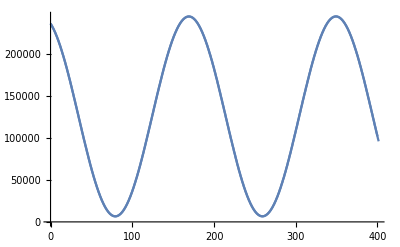

```mathematica
Show[Plot[nlmgraphg15,{theta,0,400}],ListLinePlot[{g15}]]
```

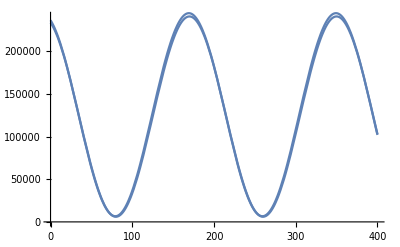

```mathematica
Show[Plot[nlmgraphg0,{theta,0,400}],Plot[nlmgraphg15,{theta,0,400}]]
```

```mathematica
550.7483710783758-370.05825107862717
```

180.69

```mathematica
deltathetag015 = 180.69011999974867 -(180)
```

0.69012

### GIALLO 2

```mathematica
nlmg2 =NonlinearModelFit[g2,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6104.54+237526. Cos[° (1276.41+theta)]^2]

```mathematica
FittedModel[6104.541747499141+237526.33319022693 Cos[° (1276.4077818105568+theta)]^2](*Funzione che descrive l'andamento di g2*)
```

FittedModel[6104.54+237526. Cos[° (1276.41+theta)]^2]

```mathematica
nlmgraphg2 = 6104.541747499141+237526.33319022693 Cos[° (1276.4077818105568+theta)]^2
```

6104.54+237526. Cos[° (1276.41+theta)]^2

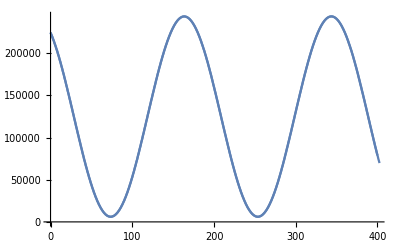

```mathematica
Show[Plot[nlmgraphg2,{theta,0,400}],ListLinePlot[{g2}]]
```

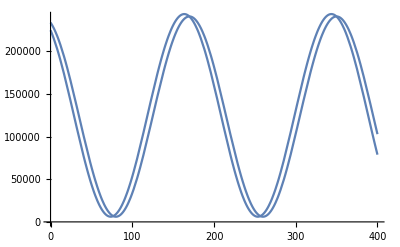

```mathematica
Show[Plot[nlmgraphg0,{theta,0,400}],Plot[nlmgraphg2,{theta,0,400}]]
```

```mathematica
1276.4077818105568-370.05825107862717
```

906.35

```mathematica
deltathetag02 = 906.3495307319297-(360+360+180)
```

6.34953

### GIALLO 3

```mathematica
nlmg3 =NonlinearModelFit[g3,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6480.41+231166. Cos[° (1638.81+theta)]^2]

```mathematica
FittedModel[6480.409150340009+231165.52622367023 Cos[° (1638.8124880297637+theta)]^2](*Funzione che descrive l'andamento di g2*)
```

FittedModel[6480.41+231166. Cos[° (1638.81+theta)]^2]

```mathematica
nlmgraphg3 = 6480.409150340009+231165.52622367023 Cos[° (1638.8124880297637+theta)]^2
```

6480.41+231166. Cos[° (1638.81+theta)]^2

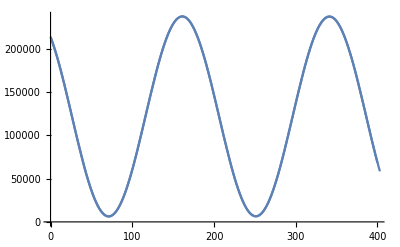

```mathematica
Show[Plot[nlmgraphg3,{theta,0,400}],ListLinePlot[{g3}]]
```

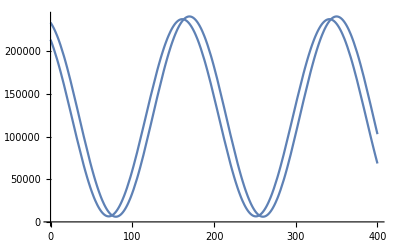

```mathematica
Show[Plot[nlmgraphg0,{theta,0,400}],Plot[nlmgraphg3,{theta,0,400}]]
```

```mathematica
1638.8124880297637-370.05825107862717
```

1268.75

```mathematica
deltathetag03 = 1268.7542369511366-(360+360+180+360)
```

8.75424

## Rosso

### ROSSO 0

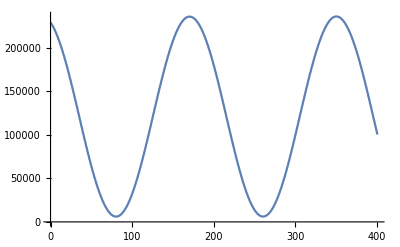

```mathematica
llpr = ListLinePlot[r0]
```

```mathematica
nlmr0 =NonlinearModelFit[r0,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6092.76+229986. Cos[° (369.716+theta)]^2]

```mathematica
FittedModel[6092.756664105353+229986.24939551332 Cos[° (369.715622623867+theta)]^2](*Funzione che descrive l'andamento di r0*)
```

FittedModel[6092.76+229986. Cos[° (369.716+theta)]^2]

```mathematica
nlmgraphr0 = 6092.756664105353+229986.24939551332 Cos[° (369.715622623867+theta)]^2
```

6092.76+229986. Cos[° (369.716+theta)]^2

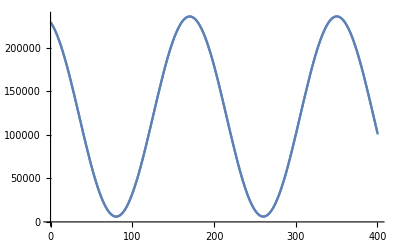

```mathematica
Show[Plot[nlmgraphr0,{theta,0,400}],ListLinePlot[{r0}]]
```

### ROSSO 1

```mathematica
nlmr1 =NonlinearModelFit[r1,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6229.42+233697. Cos[° (912.991+theta)]^2]

```mathematica
FittedModel[6229.420660136377+233696.54338079164 Cos[° (912.9912648928697+theta)]^2](*Funzione che descrive l'andamento di g1*)
```

FittedModel[6229.42+233697. Cos[° (912.991+theta)]^2]

```mathematica
nlmgraphr1 = 6229.420660136377+233696.54338079164 Cos[° (912.9912648928697+theta)]^2
```

6229.42+233697. Cos[° (912.991+theta)]^2

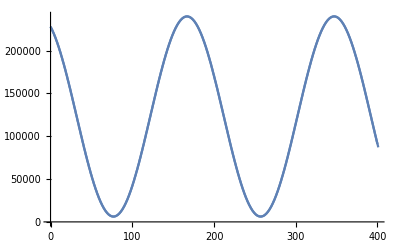

```mathematica
Show[Plot[nlmgraphr1,{theta,0,400}],ListLinePlot[{r1}]]
```

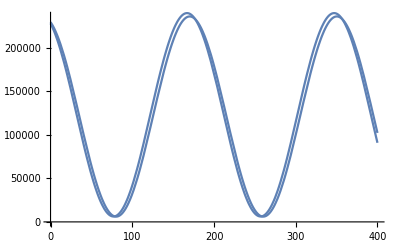

```mathematica
Show[Plot[nlmgraphr0,{theta,0,400}],Plot[nlmgraphr1,{theta,0,400}]]
```

```mathematica
912.9912648928697-369.715622623867
```

543.276

```mathematica
deltathetar01 = 543.2756422690027 -(360+180)
```

3.27564

### ROSSO 1.5

```mathematica
nlmr15 =NonlinearModelFit[r15,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6562.51+233100. Cos[° (1094.66+theta)]^2]

```mathematica
FittedModel[6562.511908183539+233099.61688035048 Cos[° (1094.6605289865636+theta)]^2](*Funzione che descrive l'andamento di g1*)
```

FittedModel[6562.51+233100. Cos[° (1094.66+theta)]^2]

```mathematica
nlmgraphr15 = 6562.511908183539+233099.61688035048 Cos[° (1094.6605289865636+theta)]^2
```

6562.51+233100. Cos[° (1094.66+theta)]^2

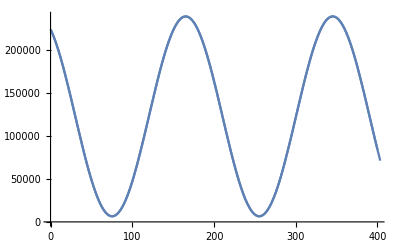

```mathematica
Show[Plot[nlmgraphr15,{theta,0,400}],ListLinePlot[{r15}]]
```

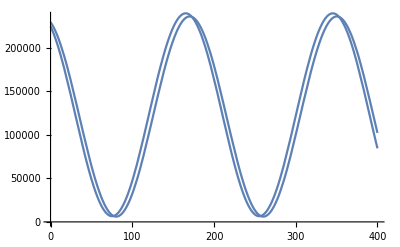

```mathematica
Show[Plot[nlmgraphr0,{theta,0,400}],Plot[nlmgraphr15,{theta,0,400}]]
```

```mathematica
1094.6605289865636-369.715622623867
```

724.945

```mathematica
deltathetar015 = 724.9449063626967 -(360+360)
```

4.94491

### ROSSO 2

```mathematica
nlmr2 =NonlinearModelFit[r2,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6127.14+233338. Cos[° (1095.49+theta)]^2]

```mathematica
FittedModel[6127.144416638138+233337.95476917998 Cos[° (1095.4923968661078+theta)]^2](*Funzione che descrive l'andamento di g1*)
```

FittedModel[6127.14+233338. Cos[° (1095.49+theta)]^2]

```mathematica
nlmgraphr2 = 6127.144416638138+233337.95476917998 Cos[° (1095.4923968661078+theta)]^2
```

6127.14+233338. Cos[° (1095.49+theta)]^2

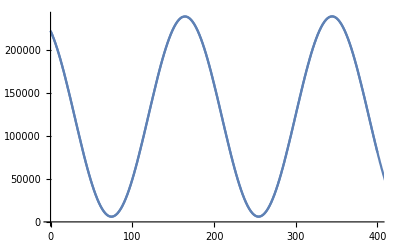

```mathematica
Show[Plot[nlmgraphr2,{theta,0,400}],ListLinePlot[{r2}]]
```

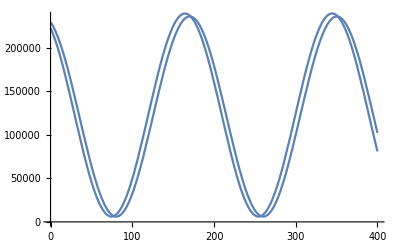

```mathematica
Show[Plot[nlmgraphr0,{theta,0,400}],Plot[nlmgraphr2,{theta,0,400}]]
```

```mathematica
1095.4923968661078-369.715622623867
```

725.777

```mathematica
deltathetar02 = 725.7767742422409 -(360+360)
```

5.77677

### ROSSO 3

```mathematica
nlmr3 =NonlinearModelFit[r3,Io (Cos[(theta+phi) Degree])^2+fondo,{Io, phi, fondo},theta]
```

FittedModel[6373.68+227176. Cos[° (1457.+theta)]^2]

```mathematica
FittedModel[6373.681290821237+227175.69462722825 Cos[° (1457.0025677955305+theta)]^2](*Funzione che descrive l'andamento di g1*)
```

FittedModel[6373.68+227176. Cos[° (1457.+theta)]^2]

```mathematica
nlmgraphr3 = 6373.681290821237+227175.69462722825 Cos[° (1457.0025677955305+theta)]^2
```

6373.68+227176. Cos[° (1457.+theta)]^2

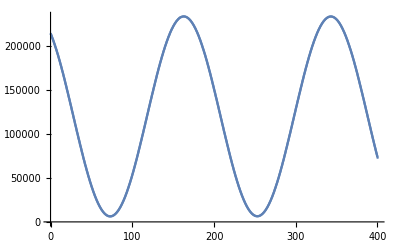

```mathematica
Show[Plot[nlmgraphr3,{theta,0,400}],ListLinePlot[{r3}]]
```

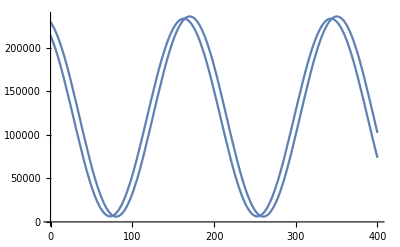

```mathematica
Show[Plot[nlmgraphr0,{theta,0,400}],Plot[nlmgraphr3,{theta,0,400}]]
```

```mathematica
1457.0025677955305-369.715622623867
```

1087.29

```mathematica
deltathetar03 = 1087.2869451716635 -(360+360+360)
```

7.28695

## Stima della costante di Verdet

```mathematica
(*Una prima cosa da stimare per poter andare a stimare la costante di verdet è il campo elettrico B. Per poterlo fare, conviene ricordare che Per un solenoide rettilineo vale la formula:*)
mu = 4 * Pi*10^(-7)
```

π/2500000

```mathematica
Nspire=3660; Lsolenoide=0.18
```

0.18

```mathematica
Bx[i_] := (mu * Nspire * i) /Lsolenoide
```

```mathematica
Vb1 = V[deltathetab01, Bx[1.]] * Pi / 180
Vb15 = V[deltathetab015, Bx[1.5]] * Pi / 180
Vb2 = V[deltathetab02, Bx[2.]] * Pi / 180
Vb3 = V[deltathetab03, Bx[3.]] * Pi / 180
Vg1 = V[deltathetag01, Bx[1.]] * Pi / 180
Vg15 = V[deltathetag015, Bx[1.5]] * Pi / 180 (*occhio, questa roba dà un valore completamente fuori scala*)
Vg2 = V[deltathetag02, Bx[2.]] * Pi / 180
Vg3 = V[deltathetag03, Bx[3.]] * Pi / 180
Vr1 = V[deltathetar01, Bx[1.]] * Pi / 180
Vr15 = V[deltathetar015, Bx[1.5]] * Pi / 180
Vr2 = V[deltathetar02, Bx[2.]] * Pi / 180
Vr3 = V[deltathetar03, Bx[3.]] * Pi / 180
```

0.000686684

0.000695708

0.000736107

0.00077269

0.00115949

0.0088119

0.001277

0.00138933

0.00123768

0.00122981

0.00140361

0.00166909